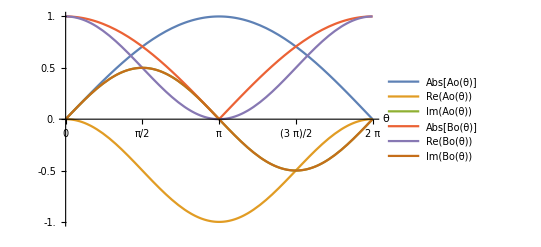

```mathematica
ClearAll["Global`*"]
Ai=0;
Bi=1;
T[θ_]:=1/2*({{1, 1}, {1, -1}}).({{ⅇ^(ⅈ θ), 0}, {0, 1}}).({{1, 1}, {1, -1}})
Ao[θ_]:={T[θ].({{Ai}, {Bi}})}[[1]][[1]][[1]]
Bo[θ_]:={T[θ].({{Ai}, {Bi}})}[[1]][[2]][[1]]
Plot[{Abs[Ao[θ]],Re[Ao[θ]],Im[Ao[θ]],Abs[Bo[θ]], Re[Bo[θ]],Im[Bo[θ]]}, {θ, 0,2π}, PlotLegends->"Expressions", AxesLabel->{θ}, Ticks->{Range[0,2π,π/4],Range[-1,1,0.5]}, GridLines->{Range[0,2π,π/4],Range[-1,1,0.5]}]
```

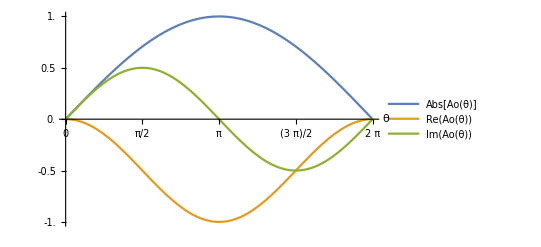

```mathematica
Plot[{Abs[Ao[θ]],Re[Ao[θ]],Im[Ao[θ]]}, {θ, 0,2π}, PlotLegends->"Expressions", AxesLabel->{θ}, Ticks->{Range[0,2π,π/4],Range[-1,1,0.5]}, GridLines->{Range[0,2π,π/4],Range[-1,1,0.5]}]
```

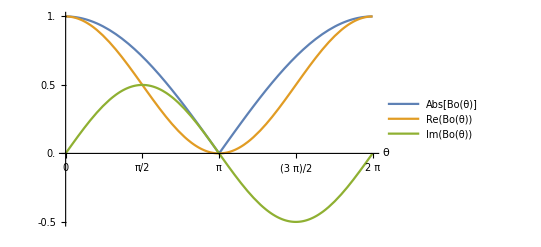

```mathematica
Plot[{Abs[Bo[θ]],Re[Bo[θ]],Im[Bo[θ]]}, {θ, 0,2π}, PlotLegends->"Expressions", AxesLabel->{θ}, Ticks->{Range[0,2π,π/4],Range[-1,1,0.5]}, GridLines->{Range[0,2π,π/4],Range[-1,1,0.5]}]
```